```mathematica
exxantiparallel=100*Table[0.001*k,{k,1,10}];
```

```mathematica
freeexxantiparallel={449.17,446.798,444.06,440.08,437.1735,432.96,428.18,422.72,416.63,409.748};
```

```mathematica
freeeyyantiparallel={448.95,446.617,444.135,441.52,438.762,435.84,432.795,429.589,426.235,422.72};
```

```mathematica
freeexxparallel={446.667,441.578,435.92,429.624,422.678,414.98,406.488,397.104,386.769,375.393};
```

```mathematica
freeeyyparallel={448.318,445.23,441.916,438.43,434.72,430.932,426.905,422.688,418.258,413.677};
```

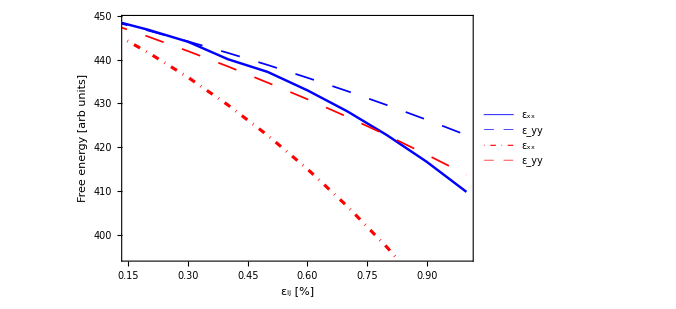

```mathematica
ListLinePlot[{
Table[{exxantiparallel[[k]],freeexxantiparallel[[k]]},{k,1,10}],
Table[{exxantiparallel[[k]],freeeyyantiparallel[[k]]},{k,1,10}],
Table[{exxantiparallel[[k]],freeexxparallel[[k]]},{k,1,10}],
Table[{exxantiparallel[[k]],freeeyyparallel[[k]]},{k,1,10}]
},
ImageSize->500,
Frame->{True,True,True,True},
PlotRangePadding->0,
PlotStyle->{
{Blue,Thickness[0.0035]},
{Blue,Dashing[Large],Thickness[0.0025]},
{Red,DotDashed,Thickness[0.0045]},
{Red,Dashing[Large],Thickness[0.0025]}
}
,PlotLegends->{"ε_xx","ε_yy","ε_xx","ε_yy"},
PlotRange->{{0.15,1.0},{395,449}},
FrameTicksStyle->Directive[Black,FontFamily->"Latin Modern Roman",18],
FrameLabel->{Style["ε_ij [%]",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->20],
Style["Free energy [arb units]",FontFamily->"Latin Modern Roman",FontColor->Black,FontSize->20]}]
```

Both structures have same volume, but the antiparallel configuration has 4500 nm^2 of domain wall, while the parallel solution has 3600 nm^2. This leads to different energies. Either the volume of the structure must be different and domain wall density the same, or the volume can be fixed and domain wall density differs. This is because the antiparallel configuration and the parallel configuration have different allowed periodic boundary conditions.

```mathematica
45*25*4
```

4500

```mathematica
36*25*4
```

3600

```mathematica
-1/(8 π^2)Normal[LeviCivitaTensor[3]]
```

{{{0,0,0},{0,0,-1/(8 π^2)},{0,1/(8 π^2),0}},{{0,0,1/(8 π^2)},{0,0,0},{-1/(8 π^2),0,0}},{{0,-1/(8 π^2),0},{1/(8 π^2),0,0},{0,0,0}}}